```mathematica
Clear["Global`*"]
```

```mathematica
r[t_] = {3Cos[3.3π*t], Sin[4π*t] + 4*t}
```

{3 Cos[10.3673 t],4 t+Sin[4 π t]}

```mathematica
r[0]
```

{3.,0}

```mathematica
track =ParametricPlot[r[t], {t, 0, 1}, AxesLabel-> {"x", "y", "z"}, PlotRange->All];
```

Find the location of the Pont; where the course crosses itself.

```mathematica
FindRoot[r[t] == r[s], {t, 0}]
```

FindRoot::nlnum: The function value {3.  - 3.\ Cos[10.3673\ s], 0.  - 4.\ s - 1.\ Sin[12.5664\ s]} is not a list of numbers with dimensions {2} at {t} = {0.}.

```mathematica
bridge = t/.FindRoot[{r[t] == r[s]},{t,0}, {s, 0.5}] (* grab the t value found from FindRoot *)
```

0.134804

```mathematica
cauchy = Graphics[Style[Disk[r[0], 0.05], Green]]; 
laplace = Graphics[Style[Disk[r[1], 0.05], Red]];
pont = Graphics[Style[Disk[r[bridge], 0.05], Yellow]];
```

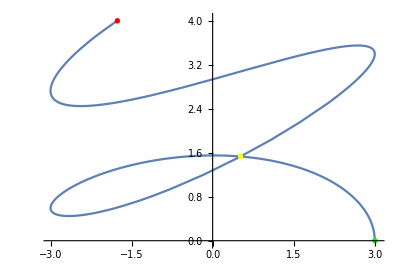

```mathematica
Show[track, cauchy, laplace, pont]
```

Speed is just the magnitude of the velocity vector at a given time, t.

```mathematica
v[t_] = r'[t];
```

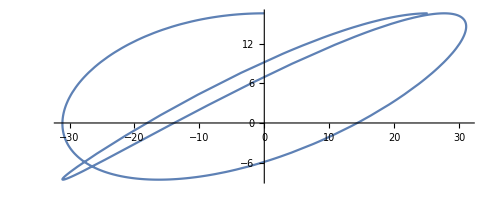

```mathematica
ParametricPlot[v[t], {t, 0, 1}]
```

The average speed is the distanced travelled (arc length 0->1) over the time it took (1hr).
Integrate the scalar magnitude of r[t] from t = 0->1 and devide by 1 hour.

```mathematica
NIntegrate[Norm[v[t]], {t, 0, 1}] (* 22.0332 km/hr *)
```

22.0332

Distance between Cauchy and Laplace. (3.)

```mathematica
dbt = EuclideanDistance[r[0],r[1]] (* 6.22009 km *)
```

6.22009